```mathematica
rules={Dispatch[…],Dispatch[…],Dispatch[<5539>],Dispatch[…],Dispatch[<5375>],Dispatch[<3731>],Dispatch[<8182>],Dispatch[<7085>]};
```

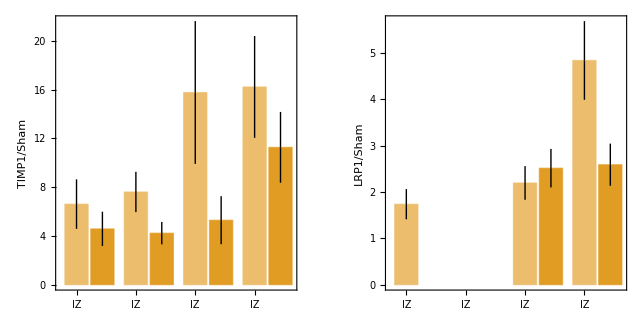

```mathematica
GraphicsRow[BarChart[Partition[(#[[2]])/(#[[1]])&/@(#/.rules),2],ChartLabels->{{"YE","YL","OE","OL"},{"IZ","BZ"}},ChartStyle->({Lighter@#,#}&/@(ColorData[97]/@Range@4)),FrameLabel->{None,ToUpperCase@#<>"/Sham"},Frame->{{True,False},{True,False}},ImageSize->Large,FrameStyle->14,AspectRatio->1,ChartLayout->"Grouped"]&/@{"timp1","lrp1"}]//Quiet
```

```mathematica
Row[Panel[TableForm[(#/.rules)/._String->{"NA","NA"},TableHeadings->{pigData[[1,2;;,1]],{"sham","MI"}}],#]&/@{"timp1","lrp1"},Spacer@10]
```

| sham | MI
YE_IZ | 7369.37 | 4.91.510^4
YE_BZ | 7369.37 | 3.41.010^4
YL_IZ | 1366.37 | 1.040.2310^4
YL_BZ | 1366.37 | 5.81.310^3
OE_IZ | 19853.1 | 3.11.210^5
OE_BZ | 19853.1 | 1.10.410^5
OL-IZ | 2501.56 | 4.11.010^4
OL-BZ | 2501.56 | 2.80.710^4timp1 | sham | MI
YE_IZ | 977.42 | 1699.318.
YE_BZ | NA | NA
YL_IZ | NA | NA
YL_BZ | NA | NA
OE_IZ | 1709.58 | 3754.620.
OE_BZ | 1709.58 | 4299.710.
OL-IZ | 3285.3 | 1.590.2810^4
OL-BZ | 3285.3 | 8.51.510^3lrp1

```mathematica
FMarkers=;
MMarkers=;
```

```mathematica
(PigCountMatrix=Uncompress@)//Dimensions
```

{31909,46}

```mathematica
genesymbols=PigCountMatrix[[2;;,1]];
```

```mathematica
dictinary=Dispatch[Rule@@@DeleteCases[Uncompress@,{_,""}]];
```

```mathematica
labels=;
```

```mathematica
geneNames=genesymbols/.dictinary;
```

```mathematica
(NormalizedData=N@(#/(Total@#))&/@(PigCountMatrix[[2;;,2;;]]ᵀ))//Dimensions
```

{45,31908}

```mathematica
FMs=((Total/@NormalizedData[[;;,Flatten[Position[ToLowerCase@geneNames,Alternatives@@#]]]])&/@{FMarkers,MMarkers})ᵀ;
```

```mathematica
ListPlot[#[[;;,;;,2]],PlotStyle->PointSize[.015],AspectRatio->1,ImageSize->Large,Frame->True,FrameLabel->{"F_I/F_R","M_I/M_R"},PlotRange->{{0.75,3},{0.25,4.75}},PlotLegends->Placed[LineLegend[{"Ag - day 3","Ag - day 28","PBS - day 3","PBS - day 28"},LegendFunction->(Framed[#,RoundingRadius->5]&)],Scaled@{.25,.85}],Axes->True,AxesOrigin->{1,1},PlotLabel->#[[1,1,1,1]]]&@(Join@@(DeleteCases[GatherBy[SortBy[{#[[2,1]],(#[[2]])/(#[[3]])&@#[[;;,2]]}&/@(Sort/@(Partition[{labels,FMs}ᵀ,3])),{#[[1,1]]&,#[[1,2]]&}],
{#[[1,1]]&,#[[1,2]]&}],
{{"Ag",_,"534 I"},_},∞]/.x:{{_String,_Real,_String},{_Real,_Real}}:>{x[[1,;;2]],Callout[x[[2]],x[[1,3]]]}))
```

-Graphics-

```mathematica
TableForm[Partition[{#[[1,1]],(Around/@(#[[;;,2]]ᵀ))ᵀ}&/@((Join@@(DeleteCases[GatherBy[SortBy[{#[[2,1]],(#[[2]])/(#[[3]])&@#[[;;,2]]}&/@(Sort/@(Partition[{labels,FMs}ᵀ,3])),{#[[1,1]]&,#[[1,2]]&}],
{#[[1,1]]&,#[[1,2]]&}],
{{"Ag",_,"534 I"},_},∞]/.x:{{_String,_Real,_String},{_Real,_Real}}:>{x[[1,;;2]],x[[2]]}))),2][[;;,;;,2]],TableHeadings->{{"Ag","PBS"},{3,28}},TableDepth->2,TableAlignments->{Center, Center}]
```

| 3 | 28
Ag | {2.870.17,3.80.4} | {1.170.17,1.060.11}
PBS | {2.40.5,3.90.7} | {1.90.4,1.390.17}

```mathematica
ListLinePlot[Callout@@@({Prepend[#,{1,1}],{"day 0","day 3","day 28"}}ᵀ)&/@Partition[(Around/@(#[[;;,2]]ᵀ))ᵀ&/@((Join@@(DeleteCases[GatherBy[SortBy[{#[[2,1]],(#[[2]])/(#[[3]])&@#[[;;,2]]}&/@(Sort/@(Partition[{labels,FMs}ᵀ,3])),{#[[1,1]]&,#[[1,2]]&}],
{#[[1,1]]&,#[[1,2]]&}],
{{"Ag",_,"534 I"},_},∞]/.x:{{_String,_Real,_String},{_Real,_Real}}:>{x[[1,;;2]],Callout[x[[2]],x[[1,3]]]}))/.Callout[x_,_]:>x),
2],
AspectRatio->1,Frame->True,PlotMarkers->{Automatic, 10},AxesOrigin->{1,1},PlotRange->All,PlotRangePadding->None,PlotLegends->Placed[{"Agrin","PBS"},Scaled@{.85,.2}]]
```

-Graphics-

```mathematica
MacGeneList=Uncompress[];
```

```mathematica
FibGeneList=Uncompress[];
```

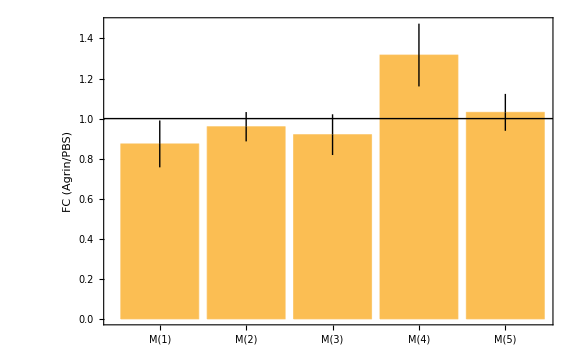
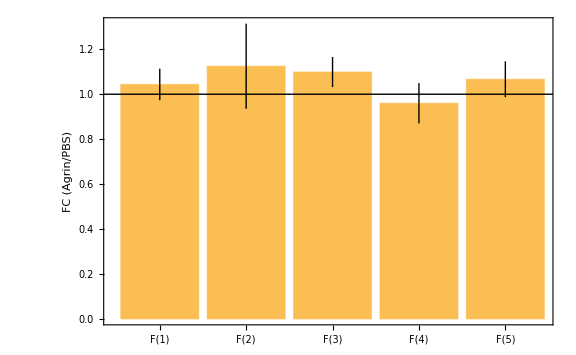

```mathematica
MapIndexed[BarChart[#,Frame->True,ChartLabels->Table[{M,F}[[#2[[1]]]][i],{i,Range@5}],ImageSize->Large,Epilog->Line[{{0.35,1},{6,1}}],FrameLabel->{Automatic,"FC (Agrin/PBS)"}]&,Partition[(#[[1]])/(#[[2]])&@((MeanAround/@(#[[;;,2]]ᵀ))&/@(DeleteCases[GatherBy[SortBy[{#[[2,1]],(#[[2]])/(#[[3]])&@#[[;;,2]]}&/@(Sort/@(Partition[{labels,Table[Total/@NormalizedData[[;;,Flatten[Position[ToLowerCase@geneNames,Alternatives@@(ToLowerCase@m)]]]],{m,Join@@{MacGeneList,FibGeneList}}]ᵀ}ᵀ,3])),{#[[1,1]]&,#[[1,2]]&}],
{#[[1,1]]&,#[[1,2]]&}],{{"Ag",_,"534 I"},_},∞][[;;,1]])),5]]
```

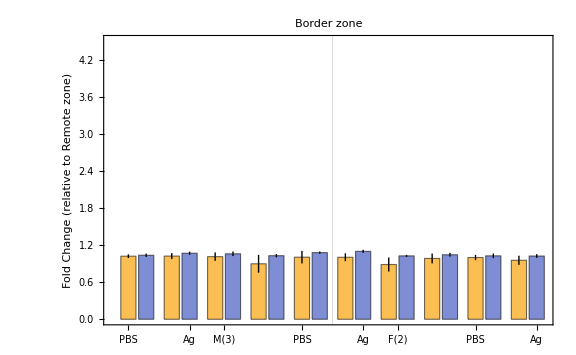
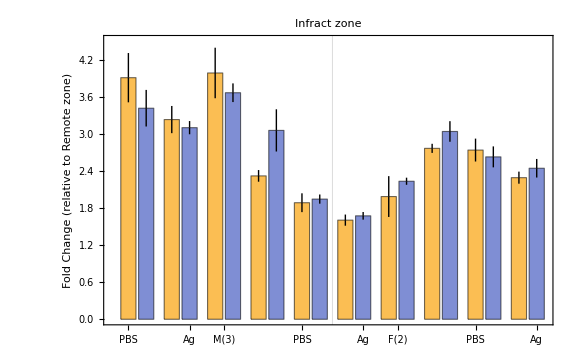

```mathematica
Row[MapIndexed[BarChart[#ᵀ,ImageSize->Large,PlotRange->{0,4.5},ChartLabels->{Join@@{M/@Range@5,F/@Range@5},{"PBS","Ag"}},PlotRangePadding->None,Frame->True,FrameLabel->{Automatic,"Fold Change (relative to Remote zone)"},PlotLabel->Style[{"Border zone","Infract zone"}[[#2[[1]]]],20],GridLines->{{12.75},None}]&,((GatherBy[SortBy[{#[[1,1,;;2]],(#[[;;2]])/(Threaded@#[[3]])&@#[[;;,2]]}&/@(Sort/@(Partition[{labels,Table[Total/@NormalizedData[[;;,Flatten[Position[ToLowerCase@geneNames,Alternatives@@(ToLowerCase@m)]]]],{m,Join@@{MacGeneList,FibGeneList}}]ᵀ}ᵀ,3])),{#[[1,1]]&,#[[1,2]]&}],
{#[[1,1]]&,#[[1,2]]&}][[{2,1},1,;;,2]]/.x:{{{_Real..}..}..}:>(Transpose/@(xᵀ))/.x:{_Real..}:>MeanAround@x)ᵀ)],
Spacer@10]
```